```mathematica
ϵ=8.85 10^-12;
μ=4 π 10^-7;
c=1/(√(ϵ μ));
L=0.130556;
a=0.0348488;
b=0.0157988;
(*l=2;*)
m=1;
k=√(((l π)/L)^2+((m π)/a)^2);
β=(l π)/L;
ω=k c;
f=(k c)/(2π);
```

```mathematica
Ex[x_,y_,z_]:=0;
Ey[x_,y_,z_]:=I(ω μ a)/(m π)Sin[(m π x)/a] Sin[(l π z)/L] ;
Ez[x_,y_,z_]:=0;


Hx[x_,y_,z_]:=(- β a)/(m π)Sin[(m π x)/a] Cos[(l π z)/L] ;
Hy[x_,y_,z_]:=0;
Hz[x_,y_,z_]:=  Cos[(m π x)/a] Sin[(l π z)/L] ;

VectorPlot3D[{Re[Hx[x,y,z]],Hy[x,y,z],Re[Hz[x,y,z]]},{x,0,a},{y,0,b},{z,-L,0},BoxRatios->{a,b,L},PlotRange->Full,VectorColorFunction->Hue];
StreamPlot[{Re[Hx[x,0,z]],Re[Hz[x,0,z]]},{x,0,a},{z,-L,0}];
```

```mathematica
w[x_,y_,z_]:=ϵ/4 (Abs[Ey[x,y,z]])^2+μ/4 ((Hz[x,y,z])^2+(Hx[x,y,z])^2);(*Energy Density, averaged aver time*)
Energy[n_]:=Integrate[w[x,y,z]/.l-> n,{x,0,a},{y,0,b},{z,0,L}]
e={};
For[i=1,i<6,i++,
	e=Append[e,Energy[i]]
	]
EyNorm[x_,y_,z_,n_]:=Abs[Ey[x,y,z]/.l-> n]/Sqrt[e[[n]]]
HzNorm[x_,y_,z_,n_]:=Abs[Hz[x,y,z]/.l-> n]/Sqrt[e[[n]]]
HxNorm[x_,y_,z_,n_]:=Abs[Hx[x,y,z]/.l-> n]/Sqrt[e[[n]]]
```

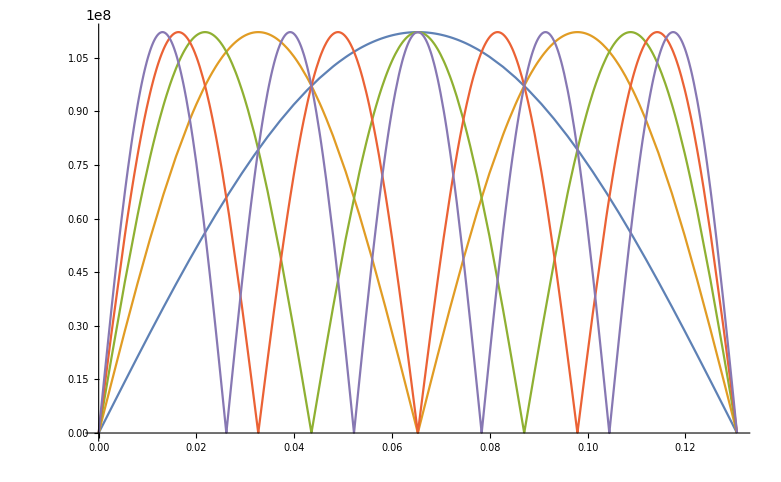

```mathematica
Plot[{EyNorm[a/2,b/2,z,1],EyNorm[a/2,b/2,z,2],EyNorm[a/2,b/2,z,3],EyNorm[a/2,b/2,z,4],EyNorm[a/2,b/2,z,5]},{z,0,L}]

Plot[{Abs[Ey[a/2,b/2,z]/.l-> 1] ,Abs[Ey[a/2,b/2,z]/.l-> 2],Abs[Ey[a/2,b/2,z]/.l-> 3],Abs[Ey[a/2,b/2,z]/.l-> 4],Abs[Ey[a/2,b/2,z]/.l-> 5]},{z,0,L}];
```